```mathematica
ClearAll["Global`*"]
```

```mathematica
PathMD="/Users/burbol/Desktop/";
input = Import[PathMD<>"Contact_Angles_sam0.dat"];
Length[input]
```

43

```mathematica
t01000=input[[{1,2,3,4,5,6,7,8,9,10},2]];
t02000=input[[{12,13,14,15,16,17,18,19,20,21},2]];
t03000=input[[{23,24,25,26,27,28,29,30,31,32},2]];
t04000=input[[{34,35,36,37,38,39,40,41,42,43},2]];
r01000=input[[{1,2,3,4,5,6,7,8,9,10},3]];
r02000=input[[{12,13,14,15,16,17,18,19,20,21},3]];
r03000=input[[{23,24,25,26,27,28,29,30,31,32},3]];
r04000=input[[{34,35,36,37,38,39,40,41,42,43},3]];
```

```mathematica
t={1,3,5,7,9,11,13,15,17,19}
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
t01t=Thread[{t,t01000}];
t02t=Thread[{t,t02000}];
t03t=Thread[{t,t03000}];
t04t=Thread[{t,t04000}]
r01t=Thread[{t,r01000}]
r02t=Thread[{t,r02000}];
r03t=Thread[{t,r03000}];
r04t=Thread[{t,r04000}];
```

{{1,145.649},{3,143.926},{5,140.225},{7,136.78},{9,137.348},{11,136.292},{13,136.196},{15,136.936},{17,135.263},{19,138.133}}

{{1,1.24166},{3,1.31983},{5,1.23156},{7,1.24421},{9,1.16979},{11,1.368},{13,1.35908},{15,1.25756},{17,1.39344},{19,1.46074}}

```mathematica
model = a
fit01t=FindFit[t01t,model,{a},x]
fit02t=FindFit[t02t,model,{a},x]
fit03t=FindFit[t03t,model,{a},x]
fit04t=FindFit[t04t,model,{a},x]
fit01r=FindFit[r01t,model,{a},x]
fit02r=FindFit[r02t,model,{a},x]
fit03r=FindFit[r03t,model,{a},x]
fit04r=FindFit[r04t,model,{a},x]
```

a

{a→140.038}

{a→136.747}

{a→138.532}

{a→138.675}

{a→1.30459}

{a→1.74289}

{a→1.92098}

{a→2.13848}

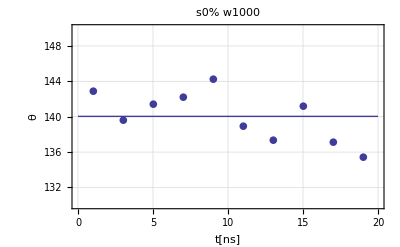

```mathematica
Show[Plot[140.03778577350002,{x,0,20}],ListPlot[t01t,PlotMarkers->{●,10}],PlotRange->{{0,20},{130,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w1000"]
```

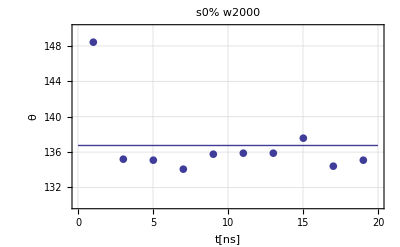

```mathematica
Show[Plot[136.74708752310002,{x,0,20}],ListPlot[t02t,PlotMarkers->{●,10}],PlotRange->{{0,20},{130,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w2000"]
```

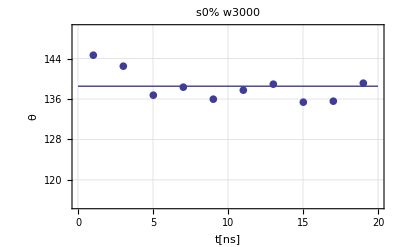

```mathematica
Show[Plot[138.53249237450004,{x,0,20}],ListPlot[t03t,PlotMarkers->{●,10}],PlotRange->{{0,20},{115,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w3000"]
```

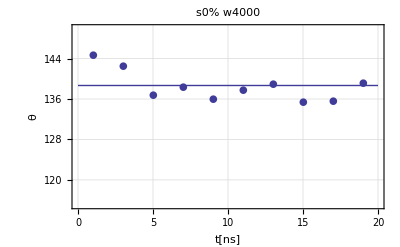

```mathematica
Show[Plot[138.67490977059998,{x,0,20}],ListPlot[t03t,PlotMarkers->{●,10}],PlotRange->{{0,20},{115,150}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w4000"]
```

```mathematica
t010002=input[[{4,5,6,7,8,9,10},2]];
t020002=input[[{15,16,17,18,19,20,21},2]];
t030002=input[[{26,27,28,29,30,31,32},2]];
t040002=input[[{37,38,39,40,41,42,43},2]];
r010002=input[[{4,5,6,7,8,9,10},3]];
r020002=input[[{15,16,17,18,19,20,21},3]];
r030002=input[[{26,27,28,29,30,31,32},3]];
r040002=input[[{37,38,39,40,41,42,43},3]];
```

```mathematica
t2={7,9,11,13,15,17,19}
```

{7,9,11,13,15,17,19}

```mathematica
t01t2=Thread[{t2,t010002}];
t02t2=Thread[{t2,t020002}];
t03t2=Thread[{t2,t030002}];
t04t2=Thread[{t2,t040002}];
r01t2=Thread[{t2,r010002}];
r02t2=Thread[{t2,r020002}];
r03t2=Thread[{t2,r030002}];
r04t2=Thread[{t2,r040002}]
```

{{7,2.21984},{9,2.15166},{11,2.19662},{13,2.23288},{15,2.1449},{17,2.24203},{19,2.05072}}

```mathematica
model2 = a2
fit01t2=FindFit[t01t2,model2,{a2},x]
fit02t2=FindFit[t02t2,model2,{a2},x]
fit03t2=FindFit[t03t2,model2,{a2},x]
fit04t2=FindFit[t04t2,model2,{a2},x]
fit01r2=FindFit[r01t2,model2,{a2},x]
fit02r2=FindFit[r02t2,model2,{a2},x]
fit03r2=FindFit[r03t2,model2,{a2},x]
fit04r2=FindFit[r04t2,model2,{a2},x]
```

a2

{a2→139.502}

{a2→135.538}

{a2→137.33}

{a2→136.707}

{a2→1.32183}

{a2→1.7772}

{a2→1.93947}

{a2→2.17695}

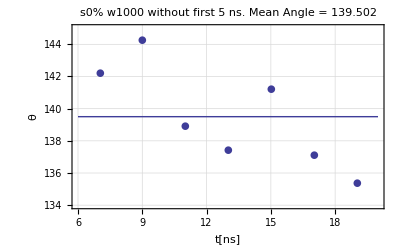

```mathematica
Show[Plot[{model2/.fit01t2},{x,6,20}],ListPlot[t01t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{134,145}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w1000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit01t2]]
```

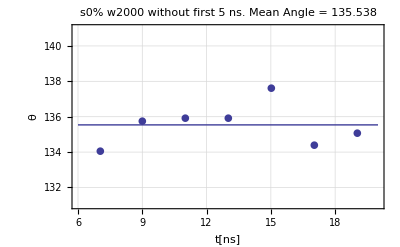

```mathematica
Show[Plot[{model2/.fit02t2},{x,6,20}],ListPlot[t02t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{131,141}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w2000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit02t2]]
```

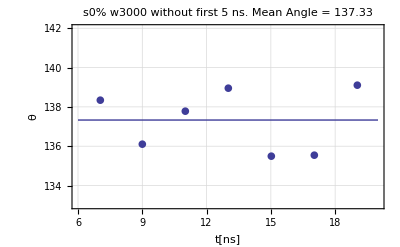

```mathematica
Show[Plot[{model2/.fit03t2},{x,6,20}],ListPlot[t03t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{133,142}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w3000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit03t2]]
```

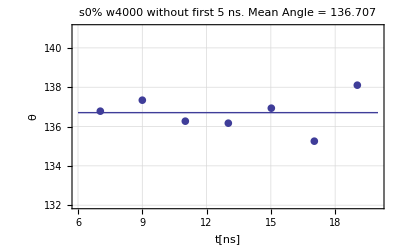

```mathematica
Show[Plot[{model2/.fit04t2},{x,6,20}],ListPlot[t04t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{132,141}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w4000 without first 5 ns. Mean Angle = "<>ToString[a2/.fit04t2]]
```

```mathematica
StandardDeviation[t01t2]
StandardDeviation[t02t2]
StandardDeviation[t03t2]
StandardDeviation[t04t2]
StandardDeviation[r01t2]
StandardDeviation[r02t2]
StandardDeviation[r03t2]
StandardDeviation[r04t2]
```

{2 √(14/3),3.17555}

{2 √(14/3),1.17912}

{2 √(14/3),1.57907}

{2 √(14/3),0.914912}

{2 √(14/3),0.101006}

{2 √(14/3),0.0598149}

{2 √(14/3),0.0843958}

{2 √(14/3),0.067319}

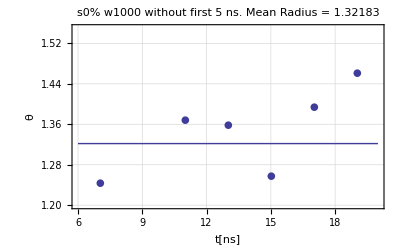

```mathematica
Show[Plot[{model2/.fit01r2},{x,6,20}],ListPlot[r01t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.2,1.55}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w1000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit01r2]]
```

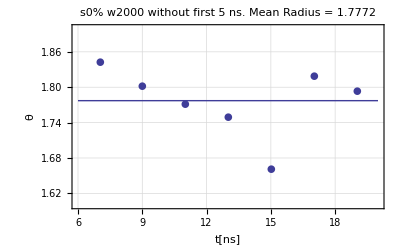

```mathematica
Show[Plot[{model2/.fit02r2},{x,6,20}],ListPlot[r02t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.6,1.9}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w2000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit02r2]]
```

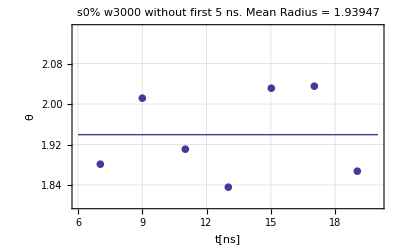

```mathematica
Show[Plot[{model2/.fit03r2},{x,6,20}],ListPlot[r03t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{1.8,2.15}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w3000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit03r2]]
```

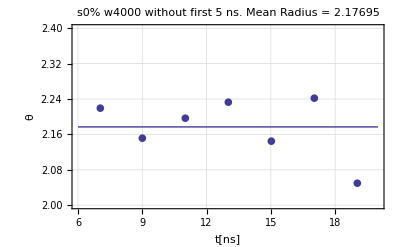

```mathematica
Show[Plot[{model2/.fit04r2},{x,6,20}],ListPlot[r04t2,PlotMarkers->{●,10}],PlotRange->{{6,20},{2.0,2.4}},GridLines->Automatic,Frame->True,FrameTicks->Automatic, AxesLabel->{"t[ns]","θ"},PlotLabel->"s0% w4000 without first 5 ns. Mean Radius = "<>ToString[a2/.fit04r2]]
```